```mathematica
SetDirectory["/Users/diwan/Documents/ICARUS/March19-pmtdata/Data2019"]
```

/Users/diwan/Documents/ICARUS/March19-pmtdata/Data2019

```mathematica
"D18_Ch_5_6_7_8_run3.h5" is bad file 
"B18_Ch_5_6_7_8_run3.h5" is bad
"B18_Ch_5_6_9_10_run1.h5" is bad  
"C16_Ch_5_6_7_8_run2.h5"; is bad
```

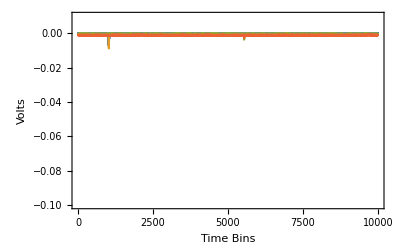

```mathematica
file1 = "C18_Ch_1_2_3_4_run3.h5"; 
file2="C18_Ch_5_6_7_8_run3.h5"; 
file3="C12_Ch_7_8_9_10_specialNoiseTestRun_2.h5"; 
file = file3; 
elements =  Import[file];
metadata  = Import[file, "RunInfo/PMTInfo"]; 
scpinfo = Import[file,"RunInfo/ScopeInfo"]; 
tst =  Import[file, "Waveforms/100"];  (* make a test plot to check *)  
ListLinePlot[{tst[[1]],tst[[2]],tst[[3]],tst[[4]]},PlotRange->{{0,10000},{-0.1,0.01}},Frame->True,FrameStyle->Bold,LabelStyle->{Bold, Medium, Italic},FrameLabel->{"Time Bins", "Volts"}]
```

```mathematica
metadata
```

{C12_C7_P69,1560,C12_C8_P66,1400,C12_C9_P78,1500,C12_C10_P114,1380}

```mathematica
scpinfo
```

{10.,10.,10.,10.,0.002,-0.0002}

```mathematica
Length[Select[elements, StringContainsQ[#,"Waveforms"]&]]
```

201

### Some constants.

```mathematica
baseline = 0;  (* subtract this from the data *)  
timeperbin = 2; 
npmts = Length[tst];  (* there are 4 traces read for each file *)  
readlength =Length[tst[[1]]];  
ntraces = Length[Select[elements, StringContainsQ[#,"Waveforms"]&]];  
(* read 100 traces *)  
voltages = {metadata[[2]],metadata[[4]],metadata[[6]],metadata[[8]]};
flanges=Flatten[Table[StringSplit[metadata,{"_","_"}][[j]][[1]],{j,{1,3,5,7}}]];
cables=Flatten[Table[StringSplit[metadata,{"_","_"}][[j]][[2]],{j,{1,3,5,7}}]];
pmtids=Flatten[Table[StringSplit[metadata,{"_","_"}][[j]][[1]],{j,{1,3,5,7}}]];
scoperanges = scpinfo[[1;;5]];
timerange = scoperanges[[5]]; 
timebin = timerange/readlength;
freqbin = 1/timerange; 
freqrange = freqbin*readlength;  (* this is twice the actual frequency range due to Nyquist *) 
electroncharge = 1.6*10^-19;
```

Part::partd: Part specification tst⟦1⟧ is longer than depth of object.

Select::normal: Nonatomic expression expected at position 1 in Select[elements,StringContainsQ[#1,Waveforms]&].

Part::partd: Part specification metadata⟦2⟧ is longer than depth of object.

Part::partd: Part specification metadata⟦4⟧ is longer than depth of object.

Part::partd: Part specification metadata⟦6⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[metadata,{_,_}].

Part::partd: Part specification metadata⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of StringSplit[metadata,{_,_}] does not exist.

Part::partw: Part 5 of StringSplit[metadata,{_,_}] does not exist.

Part::partw: Part 7 of StringSplit[metadata,{_,_}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[metadata,{_,_}].

Part::partd: Part specification metadata⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of StringSplit[metadata,{_,_}] does not exist.

Part::partw: Part 5 of StringSplit[metadata,{_,_}] does not exist.

Part::partw: Part 7 of StringSplit[metadata,{_,_}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[metadata,{_,_}].

Part::partd: Part specification metadata⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of StringSplit[metadata,{_,_}] does not exist.

Part::partw: Part 5 of StringSplit[metadata,{_,_}] does not exist.

Part::partw: Part 7 of StringSplit[metadata,{_,_}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 5 in scpinfo.

```mathematica
2^8
```

256

### write a data summary

```mathematica
Print["File name ", file]; 
Print["Traces ",  ntraces];
Print["PMts ", npmts]; 
Print["recordlength ", readlength]; 
Print["Flanges ", flanges ];
Print["Cables ", cables];
Print["PMTids ", pmtids]; 
Print["Scope Ranges ", scoperanges[[1;;4]]," mVolt fullscape"];
Print["Scope minimum bin ",scoperanges[[1;;4]]/4096, " mVolts per bit" ];
Print["Scope Time Range ",scoperanges[[5]]," sec"]; 
Print["Scope Freq bin ",freqbin," Hz"];
Print["Frequency Range ", freqrange, " Hz"];
```

File name file

Traces 2

Flanges {metadata⟦1⟧,StringSplit[metadata,{_,_}],StringSplit[metadata,{_,_}],StringSplit[metadata,{_,_}]}

Cables {metadata⟦2⟧,3,5,7}

PMTids {metadata⟦1⟧,StringSplit[metadata,{_,_}],StringSplit[metadata,{_,_}],StringSplit[metadata,{_,_}]}

Part::take: Cannot take positions 1 through 4 in scpinfo⟦1;;5⟧.

Scope Ranges scpinfo⟦1;;5⟧⟦1;;4⟧ mVolt fullscape

#### extract all the waveforms, and put them in arrays waves[[it]][[ic]]

```mathematica
allwaves = {};  
For[itr=0, itr≤ ntraces-1, itr++, 
wform = ToString[StringForm["Waveforms/``",itr]]; 
wave = Import[file, wform]; 
AppendTo[allwaves,wave]];
```

```mathematica
Length[allwaves]
```

201

```mathematica
Length[allwaves[[1]]]
```

4

### adjust the baseline by using the mean of the first 100 samples averaged over the entire data set for each pmt. The final corrections are finebaseline[[ichan]].

```mathematica
finebaseline  = Table[0,{ipmt, 1, npmts}]; 
frontbins = 1000; 
frontevts = ntraces;
```

```mathematica
sumvalues = Table[0,{ipmt,1,npmts}]; 
For[iev=1, iev<frontevts, iev++, 
(* run over all events *)
For[ipmt =1, ipmt< npmts+1,ipmt++, 
(* for each pmt channel *)  
	For[ibin=1, ibin<frontbins+1,ibin++, (* run over first 100 bins *)  
	sumvalues[[ipmt]]= sumvalues[[ipmt]]+(allwaves[[iev]][[ipmt]][[ibin]]-baseline);]]]; 
(* normalize*)  
finebaseline = N[sumvalues/(frontbins*(frontevts))]
```

{}

### We need to do the baseline subtraction in a more sophisticated way. This is because of the digitization noise which is not gaussian. It is causing the mean to be biased. We need to make a histogram for each channel and make a fit to get the mean.

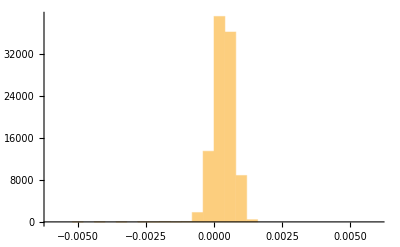
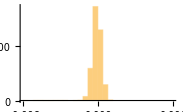
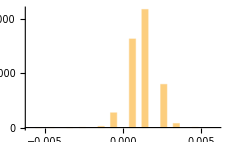
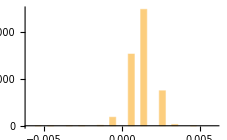

```mathematica
pedhists = Table[Histogram[Flatten[Join[Table[allwaves[[1]][[ip]],{i,1,10}]]],{-0.006,0.006,0.0004}] ,{ip,1,npmts}]
```

```mathematica
pedhistlists = Table[HistogramList[Flatten[Join[Table[allwaves[[1]][[ip]],{i,1,10}]]],{-0.006,0.006,0.0004}] ,{ip,1,npmts}];
datatable = Table[{Drop[pedhistlists[[ip]][[1]],1],pedhistlists[[ip]][[2]]},{ip,1,npmts}];
answers = Table[{},{i,1,npmts}];
as = Table[40000,{i,1,npmts}];
bs = finebaseline; 
cs=Table[2*0.002^2,{i,1,npmts}]; 
answers = Table[FindFit[Transpose[datatable[[i]]],a*Exp[-(x-b)^2/c],{{a,as[[i]]},{b,bs[[i]]},{c,cs[[i]]}},x], {i,1,npmts}]
```

General::munfl: (-1.94996×10^8)/(-6.79282468566673×10^442) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.21834×10^8)/(3.39641234283336×10^442) is too small to represent as a normalized machine number; precision may be lost.

{{a→43865.,b→-0.000234978,c→2.63362×10^-7},{a→45281.9,b→-0.000681968,c→2.44239×10^-7},{a→16673.7,b→-0.00148348,c→1.94551×10^-6},{a→19078.9,b→-0.00176163,c→1.4059×10^-6}}

```mathematica
answers[[1]]=FindFit[Transpose[datatable[[4]]],a*Exp[-(x-b)^2/c],{{a,as[[1]]},{b,bs[[1]]},{c,cs[[1]]}},x]
```

{a→19078.9,b→-0.00176163,c→1.4059×10^-6}

### Use the fitted means for the finebaseline.

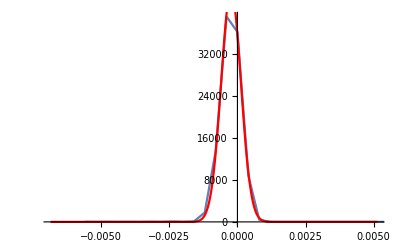
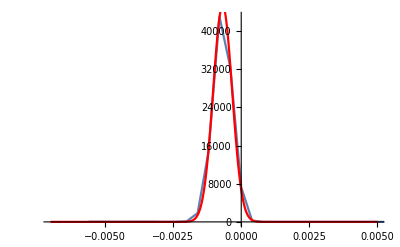
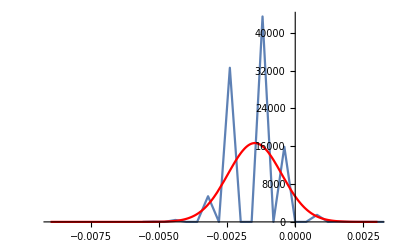
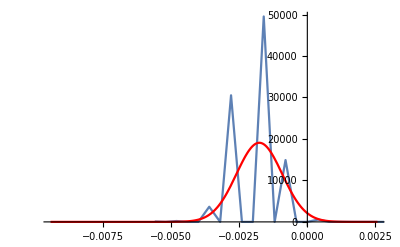

```mathematica
Table[Show[ListLinePlot[Transpose[datatable[[i]] ],PlotRange->{{bs[[i]]-0.006,bs[[i]]+0.006},Full}],Plot[a*Exp[-(x-b)^2/c]/.answers[[i]],{x,bs[[i]]-0.006,bs[[i]]+0.006},PlotStyle->Red,PlotRange->{{bs[[i]]-0.006,bs[[i]]+0.006},Full}]],{i,1,npmts}]
```

```mathematica
allmeans = Table[b/.answers[[i]],{i,1,npmts}]
```

{-0.000234978,-0.000681968,-0.00148348,-0.00176163}

```mathematica
allsigmas = Table[Sqrt[c/2]/.answers[[i]],{i,1,npmts}]
```

{0.000362878,0.000349456,0.000986284,0.000838421}

### And for some test plots to see that the data has been read properly and the baseline adjusted.

```mathematica
offset = +0.02; 
Manipulate[ListLinePlot[{(allwaves[[ie]][[1]]-finebaseline[[1]]),
(allwaves[[ie]][[2]]-finebaseline[[2]])+offset,  
(allwaves[[ie]][[3]]-finebaseline[[3]])+offset+offset,
(allwaves[[ie]][[4]]-finebaseline[[4]])+offset+offset+offset
}, 
PlotRange->{{beg,end},{bot,top}},GridLines->{Range[0,8000,200],None},ImageSize->Large,Frame->True,  FrameLabel->{"timebins","volts"},LabelStyle->Directive[Medium,Bold,Italic]],{ie,1,ntraces,1},{{beg,1},1,1000,10},{{end,10000},1,10000,10},{{bot,-0.2},-1.,1.5,0.002},{{top,0.1},0.,2.,0.002}]
```

### Perform simple analysis on the laser pulse. Simply integrate the charge between 500 and 1000 to get the total charge for each pulse. Get the mean charge for the pulses,and the standard deviation. From this get the gain.

```mathematica
lasercharge=Table[Total[allwaves[[ie]][[ip]][[600;;800]]-finebaseline[[ip]]],{ip,1,npmts},{ie,1,ntraces}] ;
```

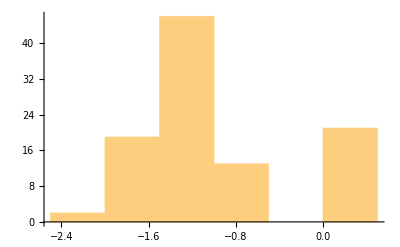

```mathematica
Histogram[lasercharge[[4]]]
```

```mathematica
lasercharge[[1]]
```

{-1.372×10^-12,-1.4396×10^-11,-2.204×10^-12,6.11995×10^-13,-1.388×10^-12,-3.388×10^-12,4.004×10^-12,2.324×10^-12,-2.0092×10^-11,-2.092×10^-12,3.556×10^-12,2.82×10^-12,-3.308×10^-12,-9.324×10^-12,-7.804×10^-12,1.924×10^-12,-8.236×10^-12,-6.076×10^-12,-1.606×10^-11,-8.732×10^-12,4.02×10^-12,-1.82×10^-12,1.716×10^-12,-5.548×10^-12,-1.98×10^-12,1.588×10^-12,-7.58×10^-12,-3.48005×10^-13,-1.606×10^-11,-1.964×10^-12,-1.054×10^-11,3.332×10^-12,-4.38×10^-12,-4.38×10^-12,-9.964×10^-12,-2.7×10^-12,1.284×10^-12,6.11995×10^-13,3.732×10^-12,4.132×10^-12,-4.92005×10^-13,-1.58×10^-12,-3.996×10^-12,2.372×10^-12,3.028×10^-12,-3.484×10^-12,-4.956×10^-12,1.188×10^-12,-5.708×10^-12,-8.348×10^-12,-1.0412×10^-11,-3.036×10^-12,-8.204×10^-12,-2.028×10^-12,-1.3036×10^-11,-2.0284×10^-11,1.79995×10^-13,-3.58×10^-12,-2.508×10^-12,1.668×10^-12,3.764×10^-12,-1.134×10^-11,3.172×10^-12,-2.252×10^-12,2.932×10^-12,2.644×10^-12,2.996×10^-12,-1.5708×10^-11,-6.20005×10^-13,-1.2076×10^-11,-9.66×10^-12,3.7×10^-12,1.78×10^-12,-2.156×10^-12,-2.012×10^-12,-5.404×10^-12,2.756×10^-12,-3.548×10^-12,1.364×10^-12,-4.14×10^-12,-1.5164×10^-11,-6.732×10^-12,3.556×10^-12,2.116×10^-12,-1.718×10^-11,-1.0364×10^-11,5.588×10^-12,4.548×10^-12,-5.74×10^-12,-9.244×10^-12,-6.7×10^-12,-4.668×10^-12,-1.1724×10^-11,-6.268×10^-12,-6.076×10^-12,-6.108×10^-12,1.236×10^-12,4.98×10^-12,-3.916×10^-12,1.572×10^-12,-3.052×10^-12}